1390

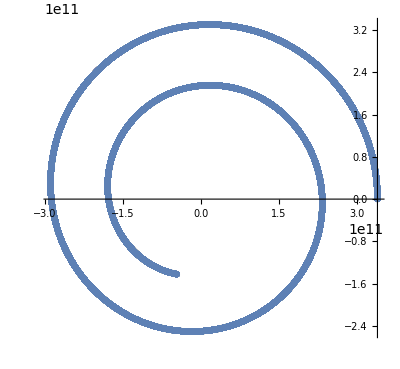

16281.4

{10.6674}

{1.496×10^11}

{1.98541×10^-7}

{-3981.08}

{29701.7}

3.68709×10^6

```mathematica
(*Initialization*)
P=2 10^6;(*Power at Belt*)
Rbelt=2.27 1.496 10^11;(*Belt distance*)
v=10^4;(*Exhaustion velocity*)
M=P/(v^2/2+19.6 10^6);(*Mass flux rate*)
tf=86400;(*Simulation step length*)
d=1000;(*Plot step length*)
rf=1.496 10^11;(*Final radius*)
F=M v;(*Thrust*)
m=10^7;(*Total mass*)
A=0;(*Initial angle*)
B=Rbelt;(*Initial radius*)
X=√((6.67384 10^-11 1.99 10^30)/Rbelt^3);(*Initial angular velocity*)
Y=0;(*Initial radial velocity*)
j=1;(*Polarplot index*)

(*Firstrun*)
s=NDSolve[{
(m-M Rbelt^2∫_0^t ⅆt/r[t]^2)(r''[t]-r[t] ϕ'[t]^2)==-(6.67384 10^-11 1.99 10^30)/r[t]^2(m-M Rbelt^2∫_0^t ⅆt/r[t]^2)-F(Rbelt/r[t])^2 r'[t]/(√(r'[t]^2+(r[t]ϕ'[t])^2)),(*Radial Newton EQ.*)
(m-M Rbelt^2∫_0^t ⅆt/r[t]^2)(r[t]ϕ''[t]+2r'[t]ϕ'[t])==-F(Rbelt/r[t])^2(r[t]ϕ'[t])/(√(r'[t]^2+(r[t]ϕ'[t])^2)) ,(*Tangential Newton EQ.*)
r[0]==B,ϕ[0]==A,r'[0]==Y,ϕ'[0]==X},
{r[t],ϕ[t],r'[t],ϕ'[t],r''[t]},{t,0,1.05tf}];(*1.05 to avoid boundary effect at 1.00*)
(*Initialization of graphic output*)
a=ParallelTable[Evaluate[r[t]/.s][[1]],{t,0,tf,d}];
b=ParallelTable[Evaluate[ϕ[t]/.s][[1]],{t,0,tf,d}];
graph={Null};
graph[[1]]=ListPolarPlot[Table[{b[[i]],a[[i]]},{i,1,Floor[tf/d]}]];
m=ParallelEvaluate[(m - M(Rbelt)^2∫_0^tf 1/r[t]^2 ⅆt) /.s][[1]]//N;
(*Initialization of boundary condition*)
A=Evaluate[ϕ[t]/.s][[1]]/.t->tf;
B=Evaluate[r[t]/.s][[1]]/.t->tf;
X=Evaluate[ϕ'[t]/.s][[1]]/.t->tf;
Y=Evaluate[r'[t]/.s][[1]]/.t->tf;
crit=Evaluate[√(r'[t]^2+r[t]^2 ϕ'[t]^2)/.s][[1]]/.t->tf;(*Exit when overspeeding or reaching earth orbit*)
(*Recursion Loop*)
While[crit<30000(*Speed limit*)&&B>rf,s=NDSolve[{
(m-M Rbelt^2∫_0^t ⅆt/r[t]^2)(r''[t]-r[t] ϕ'[t]^2)==-(6.67384 10^-11 1.99 10^30)/r[t]^2(m-M Rbelt^2∫_0^t ⅆt/r[t]^2)-F(Rbelt/r[t])^2 r'[t]/(√(r'[t]^2+(r[t]ϕ'[t])^2)),
(m-M Rbelt^2∫_0^t ⅆt/r[t]^2)(r[t]ϕ''[t]+2r'[t]ϕ'[t])==-F(Rbelt/r[t])^2(r[t]ϕ'[t])/(√(r'[t]^2+(r[t]ϕ'[t])^2)) ,
r[0]==B,ϕ[0]==A,r'[0]==Y,ϕ'[0]==X},
{r[t],ϕ[t],r'[t],ϕ'[t],r''[t]},{t,0,1.05tf}];
j++;
a=ParallelTable[Evaluate[r[t]/.s][[1]],{t,0,tf,d}];
b=ParallelTable[Evaluate[ϕ[t]/.s][[1]],{t,0,tf,d}];
graph=Append[graph,ListPolarPlot[ParallelTable[{b[[i]],a[[i]]},{i,1,Floor[tf/d]}]]];(*add graph to output list*)
(*Updating boundary condition*)
m=Evaluate[(m - M(Rbelt)^2∫_0^tf 1/r[t]^2 ⅆt) /.s][[1]]//N;
A=Evaluate[ϕ[t]/.s][[1]]/.t->tf;
B=Evaluate[r[t]/.s][[1]]/.t->tf;
X=Evaluate[ϕ'[t]/.s][[1]]/.t->tf;
Y=Evaluate[r'[t]/.s][[1]]/.t->tf;
crit=Evaluate[√(r'[t]^2+r[t]^2 ϕ'[t]^2)/.s][[1]]/.t->tf
]
Length[graph](*Number of iteration, indicating time when multiplied by tf*)
Show[graph,PlotRange->Full](*Render all graph together*)
X=FindRoot[Evaluate[r[t]/. s]==rf,{t,0.5tf}];
x=X[[All,2]][[1]]
A=ParallelEvaluate[ϕ[t]/.s][[1]]/.t->x
B=ParallelEvaluate[r[t]/.s][[1]]/.t->x(*Final angle*)
X=ParallelEvaluate[ϕ'[t]/.s][[1]]/.t->x(*Final angular velocity*)
Y=ParallelEvaluate[r'[t]/.s][[1]]/.t->x(*Final radial velocity*)
Z=ParallelEvaluate[r[t]ϕ'[t]/.s][[1]]/.t->x(*Final tangential velocity*)
m[[1]](*Mass left*)
```